## ψ_(++)(x_1,x_2), ψ_(+-)(x_1,x_2), ψ_(-+)(x_1,x_2) and ψ_(--)(x_1,x_2)

```mathematica
ψ1[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 + σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n! 2^n))HermiteH[n,(x1+x2)/(√2)];
ψ2[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 -n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ3[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ (σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(-ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ4[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(-n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!2^n))HermiteH[n,(x1+x2)/(√2)];
ψ[n_,x1_,x2_,σ1_,σ2_,θ_]:=-(ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ(σ1 + σ2 + n θ))+(ⅇ^(ⅈ 2θ))^k ⅇ^(ⅈ(σ1 -n θ))+(ⅇ^(-ⅈ 2θ))^k ⅇ^(ⅈ (σ2 + n θ))+ⅇ^(ⅈ(-n θ)))Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
```

## CHSH Inequality (without binning)

## Without Binning and Without Losses

```mathematica
Expec1[n_,x1_,x2_,σ1_,σ2_,θ_]:=
Module[{i,j,k,l,e,f,g,h},
i=ψ1[n,x1,x2,σ1,σ2,θ];
j=ψ2[n,x1,x2,σ1,σ2,θ];
k=ψ3[n,x1,x2,σ1,σ2,θ];
l=ψ4[n,x1,x2,σ1,σ2,θ];
e=Abs[i+ⅈ^2 j+ⅈ^2 k+ⅈ^4 l]^2;
f=Abs[ⅈ i+ⅈ^3 j+ⅈ k+ⅈ^3 l]^2;
g=Abs[ⅈ i+ⅈ j+ⅈ^3 k+ⅈ^3 l]^2;
h=Abs[ⅈ^2 i+ⅈ^2 j+ⅈ^2 k+ⅈ^2 l]^2;
N[(e-f-g+h)/(e+f+g+h)]];
S1[n_,x1_,x2_,θ_,a_,b_,aprime_,bprime_]:=Abs[Expec1[n,x1,x2,a,b,θ]+Expec1[n,x1,x2,a,bprime,θ]+Expec1[n,x1,x2,aprime,b,θ]-Expec1[n,x1,x2,aprime,bprime,θ]];
```

## Effects of losses

Work done in the file “Calculations for the effects of loss v3.docx”

(Assumption: ψ_(+-)(x,x) and ψ_(-+)(x,x) amplitudes are negligible after post selection on x=t_A √N)

```mathematica
f[ϕa_,ϕb_,tA_,tL_,R_]:=Module[{α,β},

α=tA ⅈ √(1-tL^2)R/(√2)ⅇ^(ⅈ ϕa);
β=tA ⅈ √(1-tL^2)R/(√2)ⅇ^(ⅈ ϕb);
ⅇ^(-(Abs[β]^2+Abs[α]^2-2β* α))];(*already squared because of two modes*)
P[m_,n_,x_,σ1_,σ2_,θ_,tA_,tL_,R_]:=Module[{outPhase,ψ,ϕ},
outPhase={{1,ⅈ^2,ⅈ^2,ⅈ^4},{ⅈ,ⅈ^3,ⅈ,ⅈ^3},{ⅈ,ⅈ,ⅈ^3,ⅈ^3},{ⅈ^2,ⅈ^2,ⅈ^2,ⅈ^2}};
ψ={outPhase[[m,1]]ψ1[n,x,x,σ1,σ2,θ],outPhase[[m,2]]ψ2[n,x,x,σ1,σ2,θ],outPhase[[m,3]]ψ3[n,x,x,σ1,σ2,θ],outPhase[[m,4]]ψ4[n,x,x,σ1,σ2,θ]};
ϕ={{-θ,-θ},{0,π},{0,π},{θ,θ}};
Abs[ ⅇ^(-(1-tA^2)R^2/4)((tA tL)^n ⅇ^((1-(tA tL)^2)R^2/2))/2]^2∑_(i=1)^4 ∑_(j=1)^4 ψ[[i]]*ψ[[j]]∑_(k=1)^2 ∑_(l=1)^2 f[ϕ[[i,k]],ϕ[[j,l]],tA,tL,R]
];
```

## Calculating the expectation value:- ⟨ab⟩

```mathematica
LossyExpec1[n_,σ1_,σ2_,θ_,tA_,tL_,R_]:=
Module[{i,j,k,l},
i=P[1,n,√n,σ1,σ2,θ,tA,tL,R];
j=P[2,n,√n,σ1,σ2,θ,tA,tL,R];
k=P[3,n,√n,σ1,σ2,θ,tA,tL,R];
l=P[4,n,√n,σ1,σ2,θ,tA,tL,R];
N[(i-j-k+l)/(i+j+k+l)]];
LossyS1[n_,θ_,a_,b_,aprime_,bprime_,tA_,tL_,R_]:=Abs[LossyExpec1[n,a,b,θ,tA,tL,R]+LossyExpec1[n,a,bprime,θ,tA,tL,R]+LossyExpec1[n,aprime,b,θ,tA,tL,R]-LossyExpec1[n,aprime,bprime,θ,tA,tL,R]];
```

## max(S) v. Photons Lost Plots

### 0 to 1 photons lost on average

```mathematica
maxOdd[n_]:=FindMaximum[S1[n,√n,√n,π/4,u,v,x,y],{u,0},{v,π},{x,(-1)^((n+1)/2+1)2},{y,(-1)^((n+1)/2+1)(-1)}];
maxEven[n_]:=FindMaximum[S1[n,√n,√n,π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}];
SvlostEven[tA_,tL_,n_]:=LossyS1[n,π/4,u,v,x,y,tA,tL,√n]/.maxEven[n][[2]];
SvlostOdd[tA_,tL_,n_]:=LossyS1[n,π/4,u,v,x,y,tA,tL,√n]/.maxOdd[n][[2]];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

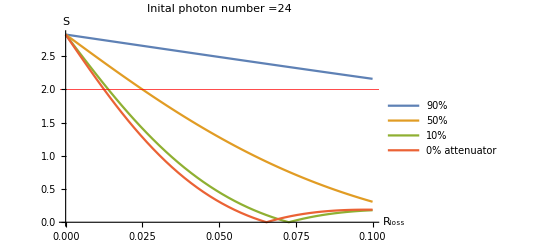

```mathematica
Plot[{SvlostEven[√0.10,√(1-Rloss),24],SvlostEven[√0.50,√(1-Rloss),24],SvlostEven[√0.90,√(1-Rloss),24],SvlostEven[√1,√(1-Rloss),24]},{Rloss,0,0.1},PlotRange->Full,GridLines->{None,{2}}, AxesStyle->Thick,LabelStyle->{FontSize->30,FontFamily->"Times",Black},AxesLabel->{"  R_loss","S"},ImageSize->Scaled[0.5],PlotStyle->Thick,PlotLegends->Placed[{"90%","50% ","10% ", "0% attenuator"},Right],GridLinesStyle->Directive[Red, Thick],PlotLabel->"Inital photon number =24"]
```

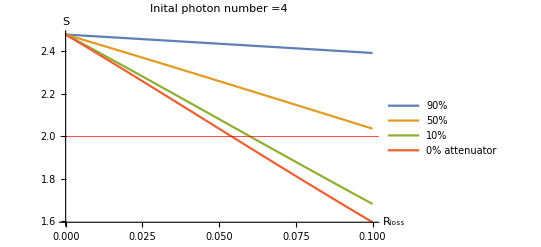

```mathematica
Plot[{SvlostEven[√0.10,√(1-Rloss),4],SvlostEven[√0.50,√(1-Rloss),4],SvlostEven[√0.90,√(1-Rloss),4],SvlostEven[√1,√(1-Rloss),4]},{Rloss,0,0.1},PlotRange->Full,GridLines->{None,{2}}, AxesStyle->Thick,LabelStyle->{FontSize->30,FontFamily->"Times",Black},AxesLabel->{"  R_loss","S"},ImageSize->Scaled[0.5],PlotStyle->Thick,PlotLegends->Placed[{"90%","50% ","10% ", "0% attenuator"},Right],GridLinesStyle->Directive[Red, Thick],PlotLabel->"Inital photon number =4"]
```

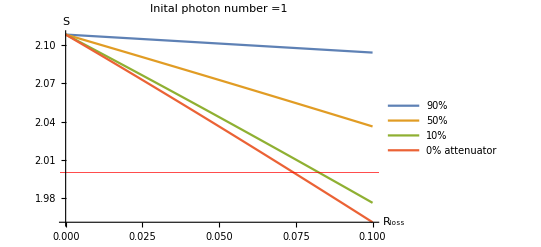

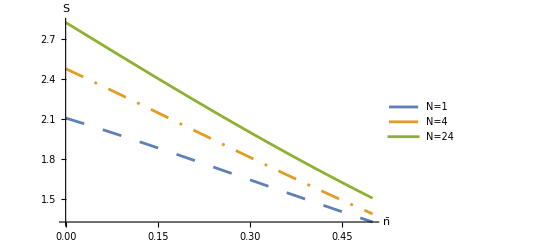

```mathematica
Plot[{SvlostOdd[√0.10,√(1-Rloss),1],SvlostOdd[√0.50,√(1-Rloss),1],SvlostOdd[√0.90,√(1-Rloss),1],SvlostOdd[√1,√(1-Rloss),1]},{Rloss,0,0.1},PlotRange->Full,GridLines->{None,{2}}, AxesStyle->Thick,LabelStyle->{FontSize->30,FontFamily->"Times",Black},AxesLabel->{"  R_loss","S"},ImageSize->Scaled[0.5],PlotStyle->Thick,PlotLegends->Placed[{"90%","50% ","10% ", "0% attenuator"},Right],GridLinesStyle->Directive[Red, Thick],PlotLabel->"Inital photon number =1"]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

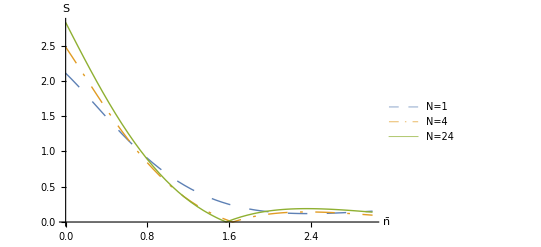

```mathematica
Plot[{SvlostOdd[lost,1],SvlostEven[lost,4],SvlostEven[lost,24]},{lost,0,3},PlotRange->Full,GridLines->{None,{2,2 √2}}, AxesStyle->Thick,LabelStyle->{FontSize->60,FontFamily->"Times",Black},AxesLabel->{"n̄","S"},ImageSize->Scaled[0.5],PlotStyle->{{Thickness[0.0025], Dashing[{Large,Large,Large,Large}]},{Thickness[0.0025],Dashing[{Large,Medium,Tiny,Medium}]},{Thickness[0.0025], Solid}},PlotLegends-> {"N=1", "N=4","N=24"}]
```